110.161

0.623626

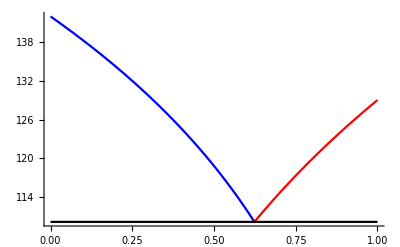

```mathematica
Pressure=3.8;

PsatA[Temp_]=10^(4.72583-1660.652/(Temp+271.5));
PsatB[Temp_]=10^(5.0768-1659.793/(Temp+227.1));

tempA[Y_]=Quiet[Temp/.Solve[PsatA[Temp]/Pressure==Y,Temp][[1]]];
tempB[Y_]=Quiet[Temp/.Solve[1-PsatB[Temp]/Pressure==Y,Temp][[1]]];

Tconstant=Temp/.FindRoot[PsatA[Temp]/Pressure==1-PsatB[Temp]/Pressure,{Temp,0}]
AzeoComp=PsatA[Tconstant]/Pressure

Show[
Plot[tempB[Z],{Z,0,AzeoComp},PlotStyle->Blue],Plot[tempA[Z],{Z,AzeoComp,1},PlotStyle->Red],Plot[Tconstant,{Z,0,1},PlotStyle->Black],PlotRange->All]
```